## Frog animation

#### Accept

```mathematica
numFrames=60
```

60

```mathematica
acceptAngles=ConstantArray[0,numFrames]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
acceptTranslation=Table[i/numFrames,{i,1,numFrames}]//N
```

{0.0166667,0.0333333,0.05,0.0666667,0.0833333,0.1,0.116667,0.133333,0.15,0.166667,0.183333,0.2,0.216667,0.233333,0.25,0.266667,0.283333,0.3,0.316667,0.333333,0.35,0.366667,0.383333,0.4,0.416667,0.433333,0.45,0.466667,0.483333,0.5,0.516667,0.533333,0.55,0.566667,0.583333,0.6,0.616667,0.633333,0.65,0.666667,0.683333,0.7,0.716667,0.733333,0.75,0.766667,0.783333,0.8,0.816667,0.833333,0.85,0.866667,0.883333,0.9,0.916667,0.933333,0.95,0.966667,0.983333,1.}

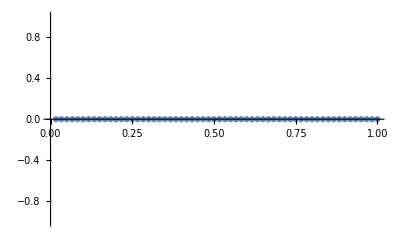

```mathematica
ListPlot[Transpose[{acceptTranslation,acceptAngles}]]
```

```mathematica
acceptLeaping=Flatten[{ConstantArray[1,numFrames*3/4],ConstantArray[0,numFrames/4]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Reject

Break this up into 4 phases: accept,

```mathematica
rejectAngles=Flatten[{ConstantArray[0,numFrames/4],Table[N[180*shakeFunction/.{x->i/(numFrames/4)}],{i,1,numFrames/4}],ConstantArray[180,numFrames/4],Table[180,{i,1,numFrames/4}]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,41.7046,17.7672,-29.1706,-73.6238,-102.283,-110.163,-97.6728,-68.4228,-27.634,18.9887,66.0127,108.752,143.527,167.766,180.,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180}

```mathematica
shakeFunction=Sqrt[x] Sin[5 Pi Sqrt[x]/2]
```

√x Sin[(5 π √x)/2]

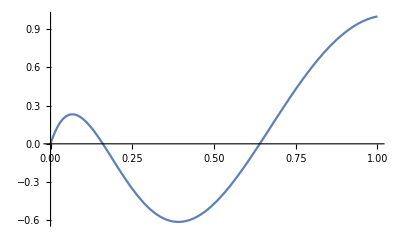

```mathematica
Plot[shakeFunction,{x,0,1}]
```

```mathematica
rejectAngles=Flatten[{ConstantArray[0,numFrames/4],Table[180*i/(numFrames/4),{i,1,numFrames/4}],ConstantArray[180,numFrames/4],Table[180,{i,1,numFrames/4}]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,24,36,48,60,72,84,96,108,120,132,144,156,168,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180,180}

```mathematica
rejectTranslations=Flatten[{Table[i/numFrames,{i,1,Floor[3/2*numFrames/4]}],Table[(3/2*numFrames/4-i)/numFrames,{i,1,Ceiling[3/2*numFrames/4]}],ConstantArray[0,numFrames/4]}]//N
```

{0.0166667,0.0333333,0.05,0.0666667,0.0833333,0.1,0.116667,0.133333,0.15,0.166667,0.183333,0.2,0.216667,0.233333,0.25,0.266667,0.283333,0.3,0.316667,0.333333,0.35,0.366667,0.358333,0.341667,0.325,0.308333,0.291667,0.275,0.258333,0.241667,0.225,0.208333,0.191667,0.175,0.158333,0.141667,0.125,0.108333,0.0916667,0.075,0.0583333,0.0416667,0.025,0.00833333,-0.00833333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Length[rejectTranslations]
```

60

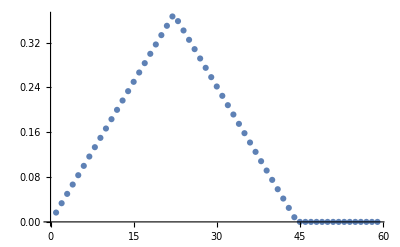

```mathematica
ListPlot[rejectTranslations]
```

```mathematica
rejectLeaping=Flatten[{ConstantArray[1,numFrames/4],ConstantArray[0,numFrames/4],ConstantArray[1,numFrames/4],ConstantArray[0,numFrames/4]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Inverse temperature mapping

Want a scaling that goes from 0 to 1 to infty

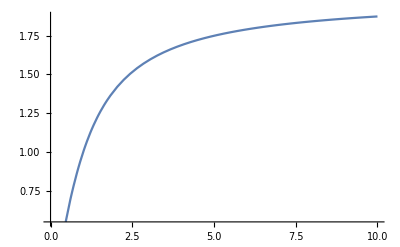

```mathematica
Plot[4/Pi ArcTan[x],{x,0,10}]
```

```mathematica
2/Pi ArcTan[1]
```

1/2

```mathematica
ArcTan[1]
```

π/4

```mathematica
Solve[y==2/Pi ArcTan[x],x]
```

{{x→ConditionalExpression[Tan[(π y)/2], ]}}

So β = tan(pi slider/2)

```mathematica
Tan[Pi/2]
```

ComplexInfinity

```mathematica
numSites=10;tempI=1;tCounts=ConstantArray[0,numSites];
```

```mathematica
Do[If[RandomReal[]>0.5,tempI+=1;If[tempI>numSites,tempI=numSites],tempI-=1;If[tempI<=0,tempI=1]];tCounts[[tempI]]+=1,{t,1,1000000}]
```

```mathematica
tCounts
```

{99759,100532,100634,100170,100459,100473,100278,100067,99176,98452}

### M&Ms

```mathematica
rawData="4
1
3
5
14
5
5
19
4
4
17
6
8
2
21
4
6
19
6
24
6
2
8
5
1
17
18
4
8
7
18
6
1
14
12
3
6
18
6
2
19
10
2
8
19
4
0
12
16
1
6
17
4
0
10
5
3
6
10
3
0
24
4
0
19
7
3
5
12
7
1
5
4
0
3
13
6
8
12
8
1
5
22
1
1
6
20
4
4
7
12
11
2
0
6
4
2
7
1
12
15
3
2
9
16
5
2
1
3
27
6
16
5
2
13
13
5
4
17
2
6
3
1
2
13
5
13
2
11
14
3
6
20
4
2
7
16
5
3
1
4
8
16
5
13
2
11
14
3
6
20
4
2
7
16
5
3
1
4
8
16
5
3
3
5
2
8
20
12
6
1
4
4
8
11
5";
```

```mathematica
mmPulls=ToExpression[StringSplit[rawData,"\n"]]
```

{4,1,3,5,14,5,5,19,4,4,17,6,8,2,21,4,6,19,6,24,6,2,8,5,1,17,18,4,8,7,18,6,1,14,12,3,6,18,6,2,19,10,2,8,19,4,0,12,16,1,6,17,4,0,10,5,3,6,10,3,0,24,4,0,19,7,3,5,12,7,1,5,4,0,3,13,6,8,12,8,1,5,22,1,1,6,20,4,4,7,12,11,2,0,6,4,2,7,1,12,15,3,2,9,16,5,2,1,3,27,6,16,5,2,13,13,5,4,17,2,6,3,1,2,13,5,13,2,11,14,3,6,20,4,2,7,16,5,3,1,4,8,16,5,13,2,11,14,3,6,20,4,2,7,16,5,3,1,4,8,16,5,3,3,5,2,8,20,12,6,1,4,4,8,11,5}

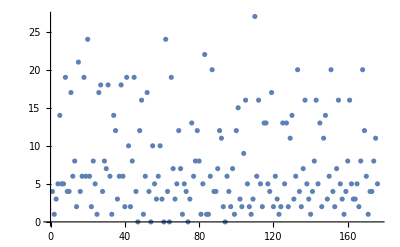

```mathematica
ListPlot[mmPulls]
```

```mathematica
Mean[mmPulls]
```

121/16

```mathematica
(mmPulls-Mean[mmPulls]).(mmPulls-Mean[mmPulls])
```

104373/16

```mathematica
autocorrelations=Table[{i-1,(mmPulls[[;;-i]]-Mean[mmPulls]).(mmPulls[[i;;]]-Mean[mmPulls])/Length[mmPulls[[;;-i]]]/((mmPulls-Mean[mmPulls]).(mmPulls-Mean[mmPulls])/Length[mmPulls])},{i,1,30}]//N
```

{{0.,1.},{1.,-0.124235},{2.,-0.337447},{3.,0.136731},{4.,0.149114},{5.,-0.155326},{6.,-0.0605107},{7.,0.196799},{8.,-0.0470597},{9.,-0.134694},{10.,0.106594},{11.,0.0613728},{12.,-0.152943},{13.,-0.0524169},{14.,0.26896},{15.,-0.0274194},{16.,-0.272089},{17.,0.0706101},{18.,0.303248},{19.,-0.200098},{20.,-0.0659614},{21.,0.1827},{22.,-0.0640272},{23.,-0.0134398},{24.,0.0936373},{25.,0.00663825},{26.,-0.0748657},{27.,0.0726259},{28.,0.0222091},{29.,-0.1059}}

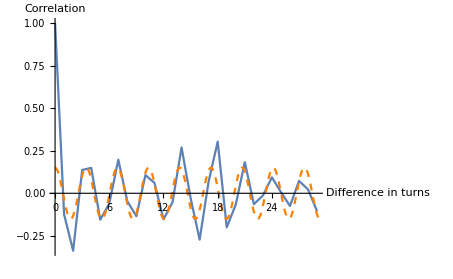

```mathematica
Show[ListLinePlot[autocorrelations,PlotRange->All,AxesLabel->{"Difference in turns","Correlation"}],Plot[0.15*Cos[2 Pi t/(3.45)],{t,0,30},PlotStyle->Directive[Orange,Dashed]]]
```

```mathematica
Table[mmPulls[[;;-i]].mmPulls[[i;;]]/,{i,1,10}]//ListPlot
```